```mathematica
Q1=(r0^2 Sinh[2a1])/(2c1);Q5=(r0^2 Sinh[2a5])/(2c5);Qp=r0^2 Sinh[2 ap]/(2 cp);
S=2Pi r0^3/Sqrt[c1 c5 cp] Cosh[a1]Cosh[a5]Cosh[ap];
M=r0^2/(2 Sqrt[c1 c5 cp])(Cosh[2a1]+Cosh[2a5]+Cosh[2ap]);
T=1/(2Pi r0 Cosh[a1]Cosh[a5]Cosh[ap]);
μ1=c1/Sqrt[c1 c5 cp] Tanh[a1];μ5=c5/Sqrt[c1 c5 cp] Tanh[a5];μp=cp/Sqrt[c1 c5 cp] Tanh[ap];
dQ1=D[Q1,a1]da1+D[Q1,r0]dr0//Simplify;
dQ5=D[Q5,a5]da5+D[Q5,r0]dr0//Simplify;
dQp=D[Qp,ap]dap+D[Qp,r0]dr0//Simplify;
dS=D[S,r0]dr0+D[S,a1]da1+D[S,a5]da5+D[S,ap]dap//Simplify;
dM=D[M,r0]dr0+D[M,a1]da1+D[M,a5]da5+D[M,ap]dap//Simplify;

dM-(T dS+μ1 dQ1+μ5 dQ5+μp dQp)//Simplify
```

0

```mathematica
N1=(r0^2 Exp[2a1])/(4 c1);
D[N1,r0]dr0+D[N1,a1]da1//Simplify
```

(ⅇ^(2 a1) r0 (dr0+da1 r0))/(2 c1)

```mathematica
1/Sqrt[2 Pi^2] Integrate[Exp[-I ω Cos[θ]] Sin[θ]^2 Sin[ϕ],{θ,0,Pi},{ϕ,0,Pi},{ψ,0,2Pi}]
```

ConditionalExpression[(2 √2 π BesselJ[1,Abs[ω]])/Abs[ω],ω∈ℝ]

```mathematica
Sqrt[4 Pi]//N
```

3.54491

```mathematica
Series[BesselJ[1,ω]/ω,{ω,0,0}]
```

1/2+O[ω]^1

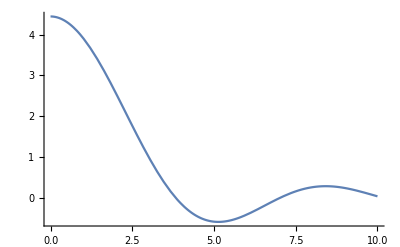

```mathematica
Plot[(2 √2 π BesselJ[1,Abs[ω]])/Abs[ω],{ω,0,10},PlotRange->All]
```

```mathematica
SphericalBesselJ[0,r]//FullSimplify
```

Sinc[r]

```mathematica
1/Sqrt[2 Pi^2]
```

1/(√2 π)

```mathematica
Integrate[Exp[-I ω Cos[θ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

(4 π Sin[ω])/ω

```mathematica
Exp[I x]/(x^(3/2)Sqrt[2 Pi^2])2 Pi^2
```

(√2 ⅇ^(ⅈ x) π)/x^(3/2)

```mathematica
R1=√((Pi ω^3)/2)(A/2+B/π(-2/(ω^2 r^2)Log[ω r]));
R2=A2 (1-r0^2/r^2)^(-I (a+b)/2)Hypergeometric2F1[-I a,-I b,1-I a-I b,(1-r0^2/r^2)];
cond1=Assuming[r0>0,Series[R2,{r0,0,1}]]
cond2=Assuming[r0>0,Series[D[R2,r],{r0,0,1}]]//Simplify
Solve[√((Pi ω^3)/2)  (A/2+B/π(-2/(ω^2 r^2)Log[ω r]))==cond1&&-(2 B)/(π r^3 ω^2)+(4 B Log[r ω])/(π r^3 ω^2)==cond2,{A,B}]
```

(A2 Gamma[1-ⅈ a-ⅈ b])/(Gamma[1-ⅈ a] Gamma[1-ⅈ b])+O[r0]^2

O[r0]^2

{{A→(2 A2 √(2/π) Gamma[1-ⅈ a-ⅈ b])/(√(ω^3) Gamma[1-ⅈ a] Gamma[1-ⅈ b]),B→0}}

```mathematica
Assuming[r0>0,cond1 Series[r^3 D[R2,r],{r0,0,2}]/.r->r0//FullSimplify]
```

(A2^2 Gamma[-ⅈ (ⅈ+a+b)]^2 (-ⅈ (a+b)+2 a b (HarmonicNumber[-ⅈ a]+HarmonicNumber[-ⅈ b])) r0^2)/(Gamma[1-ⅈ a]^2 Gamma[1-ⅈ b]^2)+O[r0]^3

```mathematica
(A2 Gamma[1-ⅈ a-ⅈ b])/(Gamma[1-ⅈ a] Gamma[1-ⅈ b])(ⅈ A2 (-(a^2+b (ⅈ+b)+a (ⅈ+2 b)) Gamma[-ⅈ (ⅈ+a+b)]+2 a b Gamma[-ⅈ (2 ⅈ+a+b)] (2 EulerGamma+Log[1/r^2]+2 Log[r0]+PolyGamma[0,1-ⅈ a]+PolyGamma[0,1-ⅈ b])) r0^2)/((ⅈ+a+b) r^3 Gamma[1-ⅈ a] Gamma[1-ⅈ b])//FullSimplify
```

(A2^2 r0^2 Gamma[-ⅈ (ⅈ+a+b)]^2 (-ⅈ (a+b)+2 a b (HarmonicNumber[-ⅈ a]+HarmonicNumber[-ⅈ b]+Log[1/r^2]+2 Log[r0])))/(r^3 Gamma[1-ⅈ a]^2 Gamma[1-ⅈ b]^2)

```mathematica
Assuming[r0>0&&r>0,Series[(1-r0^2/r^2)^(-I (a+b)/2)Hypergeometric2F1[-I a,-I b,1-I a-I b,1-r0^2/r^2],{r0,0,1}]//Normal//Simplify]
```

Gamma[-ⅈ (ⅈ+a+b)]/(Gamma[1-ⅈ a] Gamma[1-ⅈ b])

```mathematica
Assuming[r0>0&&r>0,Series[(1-r0^2/r^2)^(-I (a+b)/2)Hypergeometric2F1[-I a,-I b,1-I a-I b,1-r0^2/r^2],{r0,0,2}]//Normal//Simplify]
```

(Gamma[-ⅈ (ⅈ+a+b)] ((2 r^2+ⅈ (a+b) r0^2)/(Gamma[1-ⅈ a] Gamma[1-ⅈ b])+(2 r0^2 (-1+2 EulerGamma-2 Log[r]+2 Log[r0]+PolyGamma[0,1-ⅈ a]+PolyGamma[0,1-ⅈ b]))/(Gamma[-ⅈ a] Gamma[-ⅈ b])))/(2 r^2)

```mathematica
D[B/π(-2/(ω^2 r^2)Log[ω r]),r]
```

-(2 B)/(π r^3 ω^2)+(4 B Log[r ω])/(π r^3 ω^2)

```mathematica
Solve[√((Pi ω^3)/2)  (A/2+B/π(-2/(ω^2 r^2)Log[ω r]))==Gamma[-ⅈ (ⅈ+a+b)]/(Gamma[1-ⅈ a] Gamma[1-ⅈ b])&&-(2 B)/(π r^3 ω^2)+(4 B Log[r ω])/(π r^3 ω^2)==0,{A,B}]
```

{{A→(2 √(2/π) Gamma[-ⅈ (ⅈ+a+b)])/(√(ω^3) Gamma[1-ⅈ a] Gamma[1-ⅈ b]),B→0}}

```mathematica
Solve[(z^(-1/2 ⅈ (a+b)) Gamma[-ⅈ (ⅈ+a+b)])/(Gamma[1-ⅈ a] Gamma[1-ⅈ b])
```

```mathematica
h[r]/r^(d-1)D[h[r] r^(d-1)D[R[r],r],r]//Simplify
r^((d-1)/2)h[r]/r^(d-1)D[h[r] r^(d-1)D[r^(-(d-1)/2)ψ[r],r],r]//Simplify
```

(h[r] (r h'[r] R'[r]+h[r] ((-1+d) R'[r]+r R''[r])))/r

(h[r] (2 r h'[r] (ψ[r]-d ψ[r]+2 r ψ'[r])+h[r] (-(3-4 d+d^2) ψ[r]+4 r^2 ψ''[r])))/(4 r^2)

```mathematica
1/r^3 D[r^3 D[R[r],r],r]//Simplify
r^(3/2)h[r]/r^3 D[h[r] r^3 D[r^(-3/2)ψ[r],r],r]//Expand
```

(3 R'[r])/r+R''[r]

-(3 h[r]^2 ψ[r])/(4 r^2)-(3 h[r] ψ[r] h'[r])/(2 r)+h[r] h'[r] ψ'[r]+h[r]^2 ψ''[r]

```mathematica
r^((d-1)/2)h[r]/r^(d-1)D[h[r] r^(d-1)D[r^(-(d-1)/2)ψ[r],r],r]-h[r]D[h[r] D[ψ[r],r],r]//Simplify
```

```mathematica
-((-1+d) h[r] ((-3+d) h[r]+2 r h'[r]))/(4 r^2)/.h[r]->1-r0^(d-2)/r^(d-2)/.h'[r]->D[1-r0^(d-2)/r^(d-2),r]//Expand
```

-3/(4 r^2)+d/r^2-d^2/(4 r^2)+1/2 r^-d r0^(-2+d)-1/2 d r^-d r0^(-2+d)+1/4 r^(2-2 d) r0^(-4+2 d)-1/2 d r^(2-2 d) r0^(-4+2 d)+1/4 d^2 r^(2-2 d) r0^(-4+2 d)

```mathematica
-2 (2-d) r^(2-d) r0^(-2+d)+(-3+d) (1-r^(2-d) r0^(-2+d))//Simplify
```

-3+d+(-1+d) r^(2-d) r0^(-2+d)

```mathematica
DSolve[ψ''[ρ]+(1-((d-1)(d-3))/(4 ρ^2))ψ[ρ]==0,ψ,ρ]
```

{{ψ→Function[{ρ},√ρ BesselJ[1/2 (-2+d),ρ] C[1]+√ρ BesselY[1/2 (-2+d),ρ] C[2]]}}

```mathematica
-3+4d-d^2//Factor
```

-(-3+d) (-1+d)

```mathematica
-1/2 ν Pi -1/4 Pi/.ν->-1+d/2//Simplify
```

1/4 (π-d π)

```mathematica
Sqrt[c/(24 Δ)]Δ+1/Sqrt[c/(24 Δ)] c/24//Simplify
```

(√(c/Δ) Δ)/(√6)

```mathematica
Sqrt[c/(24 (Δ-c/24))](Δ-c/24)+Sqrt[(c/(24 (Δ-c/24)))^-1] c/24//Simplify
```

√(-c/(c-24 Δ)) (-c/24+Δ)+1/24 c √(-1+(24 Δ)/c)

```mathematica
DSolve[(1-r0^(d-2)/r^(d-2))/r^(d-1)D[(1-r0^(d-2)/r^(d-2)) r^(d-1) D[R[r],r],r]+ω^2 RH^(2(d-1))/r^(2(d-1))R[r]==0,R,r]
```

{{R→Function[{r},C[1] Cos[(r0^(2-d) RH^(-1+d) ω Log[r0^2-r^(2-d) r0^d])/(-2+d)]-C[2] Sin[(r0^(2-d) RH^(-1+d) ω Log[r0^2-r^(2-d) r0^d])/(-2+d)]]}}

```mathematica
Exp[-I (r0^(2-d) RH^(-1+d) ω Log[1-r^(2-d) r0^(d-2)])/(-2+d)]
```

(1-r^(2-d) r0^(-2+d))^(-(ⅈ r0^(2-d) RH^(-1+d) ω)/(-2+d))

```mathematica
Series[(1+q)^8/(1-q)^8((1+q^2)^8)/((1-q^2)^8)((1+q^3)^8)/((1-q^3)^8)((1+q^4)^8)/((1-q^4)^8),{q,0,4}]
```

1+16 q+144 q^2+960 q^3+5264 q^4+O[q]^5

```mathematica
1
2^4
2 2^4+(2^8-2 2^4)/2
3 2^4+((2^4)^3-3 2^4-3 2^4 2^4)/6
```

1

16

144

1784/3

```mathematica
3 2^4+(3 2^4 2^4)/2 +((2^4)^3-3 2^4 2^4-3 2^4)/(3 2)
```

2936/3

```mathematica
(Series[BesselJ[-1+d/2,x],{x,0,0}]//Normal)/.x->r  ω
(Series[BesselY[-1+d/2,x],{x,0,0}]//Normal)/.x->r  ω
```

(2^(1-d/2) (r ω)^(-1+d/2))/Gamma[d/2]

-(2^(1-d/2) (r ω)^(-1+d/2) Cos[(-1+d/2) π] Gamma[1-d/2])/π

```mathematica
Series[BesselJ[-1+d/2,x],{x,0,0}]//Normal//Simplify
Series[BesselY[1,x],{x,0,0}]//Normal//Simplify
```

(2^(1-d/2) x^(-1+d/2))/Gamma[d/2]

-2/(π x)